# Finite Difference Reversible CV

## Fully implicit method

This notebook shows how a cyclic voltammogram for the simple reversible reaction A + e ⇌ B can be simulated using implicit finite difference methods.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
cvTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];

cvTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},
FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
Frame->True,
FrameLabel->{
Style["increment",FontFamily->"Arial" ,FontSize-> 12,FontColor->Black],
StyleForm["√πχ",FontFamily-> "Times New Roman" ,FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None},
FrameTicks-> {Automatic,cvTicks2,Automatic,cvTicks4},
Joined->True,
PlotRange->{{0,All},{-0.5,0.4}},
PlotStyle->{Red,AbsoluteThickness[0.5]}};
```

```mathematica
optionB={
Frame->True,
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["√πχ",FontFamily->  "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None},
Joined->True,
PlotRange->{All,{-0.5,0.4}},
PlotStyle->{Red,AbsoluteThickness[0.5]}};
```

```mathematica
optionC={
FrameTicks-> {None,Automatic,None,None},
PlotStyle->{{Red,AbsoluteThickness[0.5]},{Blue,AbsoluteThickness[0.5]}},
PlotRange->{{1,All},{0.,1.0}}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeDiagonals];

makeDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-d,{m-3}];
		z=Table[-d,{m-3}];
		y=Table[1.+2.*d,{m-2}];
{x,y,z}]
```

```mathematica
{x,y,z}=makeDiagonals[7,𝔻]
```

{{-𝔻,-𝔻,-𝔻,-𝔻},{1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻},{-𝔻,-𝔻,-𝔻,-𝔻}}

## Set Up Solution

### LinearSolve Solution

```mathematica
Clear[implicitSolveCV];

implicitSolveCV[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_}]:=Module[{x,y,z,len,mat,initial,range,ξ,τ,solveNext},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1)//N (*calculation of the incremental time/potential step*);
ξ[k_]:=If[k>(n+1)/2,Exp[(upperLimit-range+(τ*(k-1)))],Exp[(upperLimit-(τ*(k-1)))]];

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext[list_List,j_Integer]:=Module[{b},
b=list⟦2;;-2⟧;
b⟦1⟧+=d*ξ[j]/(1.+ξ[j]);
b[[-1]]+=d;
Flatten[{ξ[j]/(1.+ξ[j]),LinearSolve[mat,b],1.}]];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Simulation variables

```mathematica
Clear[upperLimit,lowerLimit,𝕥,n,𝔻,τ,m];

lowerLimit=-8.(*limit = f×(E-E^o)*);
upperLimit=8.(*limit = f×(E-E^o)*);
𝕥=2.*(upperLimit+Abs[lowerLimit]);
n=401;
𝔻=2.;
τ=𝕥/(n-1) (*calculation of the incremental time/potential step*);
m=1+Ceiling[6*√(𝔻*(n-1))];
```

## Solve

LinearSolve solution

```mathematica
Clear[c];

Timing[
c=implicitSolveCV[m,n,𝔻,{lowerLimit,upperLimit}];
Rest[c];
]
```

{0.083722,Null}

## Plot CV

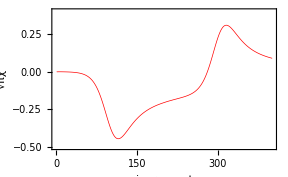

```mathematica
cv1=Map[((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)*√(𝔻*(n-1))/√(𝕥*4))&,c];
plot1=ListPlot[cv1,optionA]
```

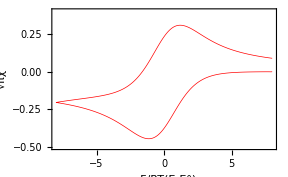

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+((j-1)*τ),upperLimit-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionB]
```

## Animation of Concentration Profiles

This calculation can be animated to see how the concentration profile changes with time.

```mathematica
animation=Animate[ListPlot[{c⟦j⟧,1.-#&/@c⟦j⟧},optionC], {j, 1,n, 10}]
```

```mathematica
(*save as an animated GIF file with the animation looping 5 times*)

Export["conc.gif",Table[ListPlot[{c⟦j⟧,1.-#&/@c⟦j⟧},optionC], {j, 1,n, 10}],"AnimationRepetitions"-> 5]
```

conc.gif

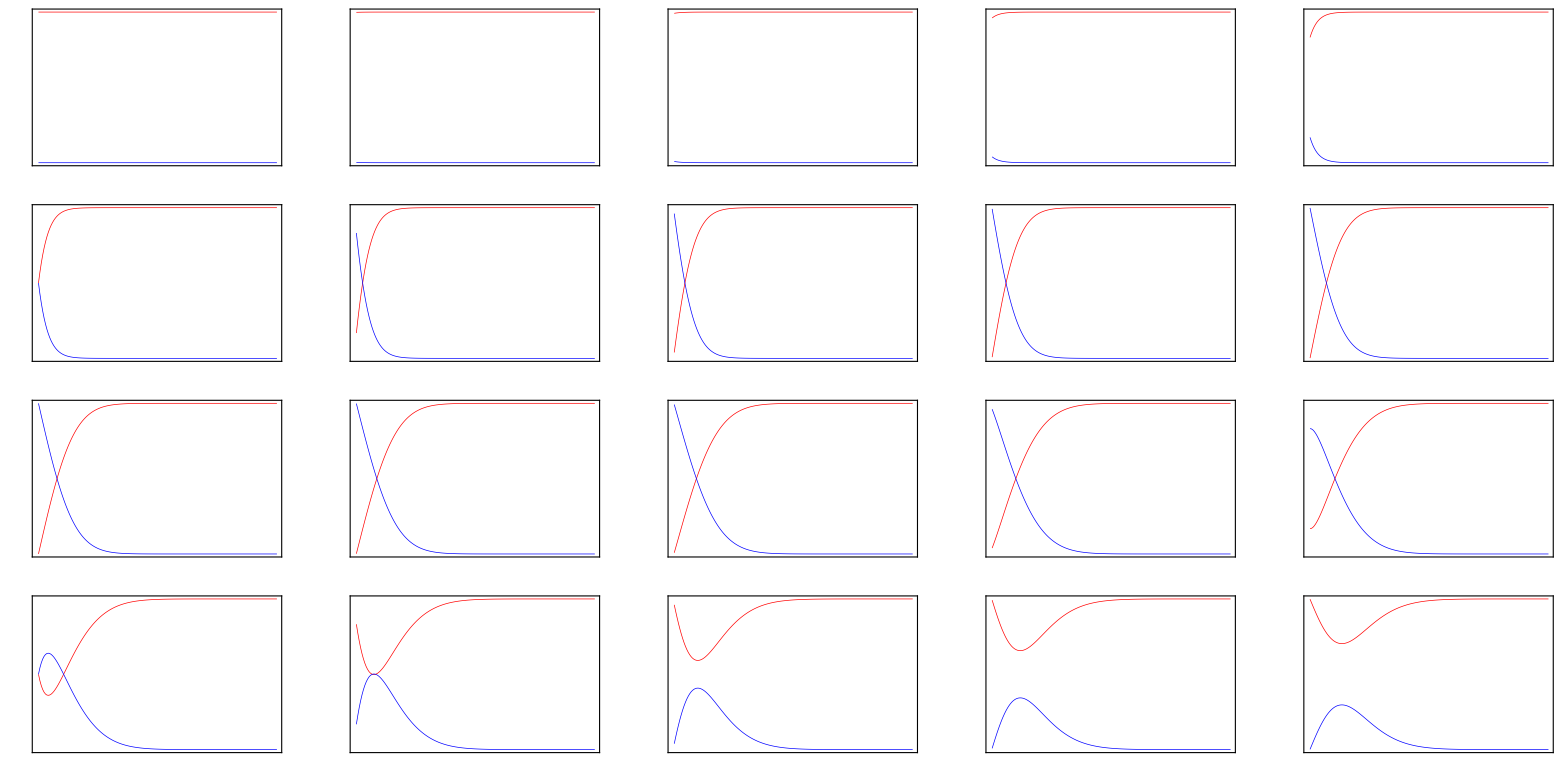

```mathematica
Table[ListPlot[{c⟦j,All⟧,1.-#&/@c⟦j,All⟧},
FrameTicks-> None,
PlotStyle->{{Red,AbsoluteThickness[0.5]},{Blue,AbsoluteThickness[0.5]}},
DisplayFunction-> Identity], {j, 1,n,20}];
Show[GraphicsGrid[Partition[%,5]]]
```